```mathematica
Clear["Global`*"];
adagfxn[n_,m_] := N[Sqrt[m]] /; m-n == 1;
adagfxn[n_,m_] := 0. /; m-n ≠ 1;
adag[basissize_] := Table[adagfxn[n,m],{n,0,basissize-1},{m,0,basissize-1}];
a[basissize_] := ConjugateTranspose[adag[basissize]];
x[basissize_] := Sqrt[1 / 2.](a[basissize] + adag[basissize]);
p[basissize_] := -I Sqrt[2.] (a[basissize] -  adag[basissize]);
h0[basissize_] := DiagonalMatrix[Table[n + 1 / 2,{n, 0, basissize - 1}]] ;
H[basissize_]:= h0[basissize]
S[basissize_] := Transpose[Normalize /@ Eigenvectors[x[basissize]]];
fn[basissize_,n_] := Sort[Eigenvalues[N[H[basissize]]]][[n]];
toposbasis[basissize_,evec_]:= ConjugateTranspose[S[basissize]].evec;
xvals[basissize_]:= Table[(ConjugateTranspose[S[basissize]].x[basissize].S[basissize])[[m]][[m]],{m,basissize}];
V[x_]:= x^2/2;
```

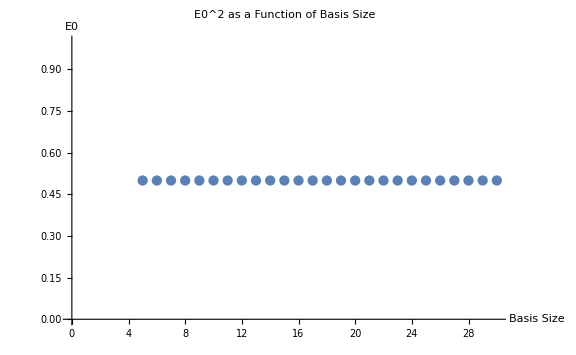

```mathematica
n = 0; 
ListPlot[Table[{basissize,fn[basissize,n+1]},{basissize,5,30}],PlotLabel->"E0^2 as a Function of Basis Size",AxesLabel->{"Basis Size","E0"},ImageSize->Large]
```

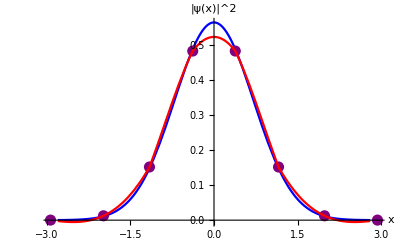

```mathematica
n = 0; bs = 8;
{evals,evecs} = Eigensystem[N[H[bs]]];
{evals,evecs} = Transpose@SortBy[Transpose[{evals,evecs}],First];
e0 = Chop[evals[[n+1]]];
e0wf = Chop[evecs[[n+1]]];
energy[e0_,x_] := e0 /; e0 ≥ V[x];
h0eigenfxn[n_,x_] := N[(2^n Factorial[n] Sqrt[Pi])^(-1 / 2) Exp[-x^2 / 2] HermiteH[n,x]];
fun = Interpolation[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wf]]^2}]];
norm2 = NIntegrate[fun[x],{x,-2.8,2.8}];
p1 = Plot[Abs[h0eigenfxn[n,x]]^2,{x,-2.8,2.8},PlotStyle->Blue];
p2 = ListPlot[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wf]]^2/norm2}],PlotStyle->{AbsolutePointSize[8],Purple}];
p3 = Plot[fun[x]/norm2,{x,-2.8,2.8},PlotStyle->Hue[1]];
plot = Show[p1,p2,p3,AxesLabel->{"x","|ψ(x)|^2"},PlotRange->All];
Needs["PlotLegends`"]
ShowLegend[plot,{{{Graphics[{Purple, Disk[{0,0},.05]}],"Discrete"},{Graphics[{Thickness[.1],Red,Line[{{0,0},{2,0}}]}],"Interpolation"},{Graphics[{Thickness[.1],Blue,Line[{{0,0},{2,0}}]}],"Actual"}},LegendPosition->{0.2,0.1},LegendSize->{0.6,0.4},LegendShadow->False}]
```

```mathematica
K = ConjugateTranspose[S[5]].MatrixExp[-I H [5](.1-0)].S[5];
Chop[K]//MatrixForm
```

(0.945324-0.312664 ⅈ | -0.00312634-0.00531916 ⅈ | 0.0247509+0.0848469 ⅈ | -0.005619-0.00992025 ⅈ | -0.0113811-0.0222148 ⅈ
-0.00312634-0.00531916 ⅈ | 0.945324-0.312664 ⅈ | 0.005619+0.00992025 ⅈ | -0.0247509-0.0848469 ⅈ | -0.0113811-0.0222148 ⅈ
0.0247509+0.0848469 ⅈ | 0.005619+0.00992025 ⅈ | 0.967236-0.209866 ⅈ | 0.0124571+0.0248757 ⅈ | 0.0239618+0.105456 ⅈ
-0.005619-0.00992025 ⅈ | -0.0247509-0.0848469 ⅈ | 0.0124571+0.0248757 ⅈ | 0.967236-0.209866 ⅈ | -0.0239618-0.105456 ⅈ
-0.0113811-0.0222148 ⅈ | -0.0113811-0.0222148 ⅈ | 0.0239618+0.105456 ⅈ | -0.0239618-0.105456 ⅈ | 0.971133-0.179623 ⅈ)

```mathematica
Abs[K]^2 // MatrixForm
xvals[5]
```

(0.991397 | 0.0000380674 | 0.0078116 | 0.000129985 | 0.000623027
0.0000380674 | 0.991397 | 0.000129985 | 0.0078116 | 0.000623027
0.0078116 | 0.000129985 | 0.979589 | 0.000773979 | 0.0116952
0.000129985 | 0.0078116 | 0.000773979 | 0.979589 | 0.0116952
0.000623027 | 0.000623027 | 0.0116952 | 0.0116952 | 0.975363)

{2.02018,-2.02018,0.958572,-0.958572,4.93038×10^-32}

```mathematica
Kmat[basissize_,T_, t_]:= ConjugateTranspose[S[basissize]].MatrixExp[-I H [basissize](T-t)].S[basissize];
probabilities[basissize_,T_, t_]:= Abs[Kmat[basissize,T, t]]^2;
Kan[xf_,tf_]:= Sqrt[1/(2 Pi I Sin[tf])] Exp[I ((xf^2 +1.98166^2) Cos[tf] - 2(-1.98166) xf)/(2 Sin[tf])];
```

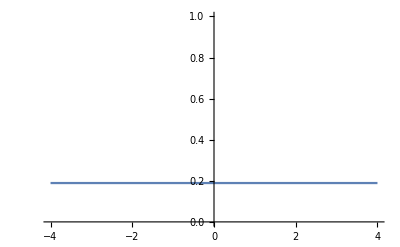

```mathematica
bas = 8; T = 1; t = 0; xx = 3;
p1 = ListPlot[Transpose[{xvals[bas],probabilities[bas,T,t][[xx]]}],PlotLabel-> StringForm["xi = ``, ti = ``, tf = ``",xvals[bas][[xx]],t,T],AxesLabel->{"x","Prob(xi,ti to x,tf)"},PlotRange-> {{-4,4},{0,1}}];
p2 = Plot[Abs[Kan[xvv,1]]^2,{xvv,-4,4},PlotRange-> {{-4,4},{0,1}}]
animation = Table[ListPlot[Transpose[{xvals[bas],probabilities[bas,TF/10,t][[xx]]}],PlotLabel-> StringForm["xi = ``, ti = ``, tf = ``",xvals[bas][[xx]],t,N[TF/10]],AxesLabel->{"x","Prob(xi,ti to x,tf)"},PlotRange-> {{-4,4}{0,0.25}}],{TF,0,100}];
ListAnimate[animation,4]
```

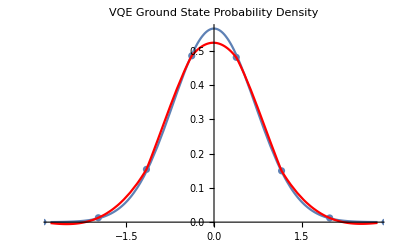

```mathematica
n = 0; bs = 8;
e0wf = {0.9984025559105432,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
e0wf = {Cos[-.0042],Sin[-.0042],0.0,0.0,0.0,0.0,0.0,0.0};
h0eigenfxn[n_,x_] := N[(2^n Factorial[n] Sqrt[Pi])^(-1 / 2) Exp[-x^2 / 2] HermiteH[n,x]];
fun = Interpolation[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wf]]^2}]];
norm2 = NIntegrate[fun[x],{x,-2.8,2.8}];
p1 = Plot[Abs[h0eigenfxn[n,x]]^2,{x,-2.8,2.8}];
p2 = ListPlot[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wf]]^2/norm2}]];
p3 = Plot[fun[x]/norm2,{x,-2.8,2.8},PlotStyle->Hue[1]];
Show[p1,p2,p3,PlotLabel-> "VQE Ground State Probability Density"]
```

```mathematica
(*Zeros test*)
wavefxn[n_,x_] := Sqrt[2] Sin[n Pi x];
xop = Table[Integrate[wavefxn[n1,x] x wavefxn[n2,x],{x,0,1}],{n2,10},{n1,10}];
vals = Eigenvalues[xop];
```

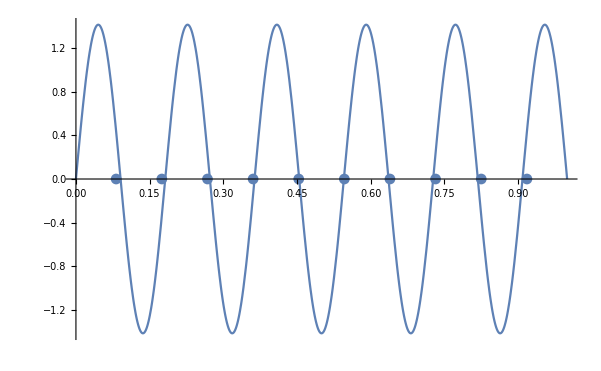

```mathematica
p1 = Plot[wavefxn[11,x],{x,0,1}];
p2 = ListPlot[Transpose[{vals,{0,0,0,0,0,0,0,0,0,0}}]];
Show[p1,p2]
```

```mathematica
h0eigenfxn[n_,x_] := N[(2^n Factorial[n] Sqrt[Pi])^(-1 / 2) Exp[-x^2 / 2] HermiteH[n,x]];
xop = Table[Integrate[h0eigenfxn[n1,x] x h0eigenfxn[n2,x],{x,-100,100}],{n2,0,9},{n1,0,9}];
vals = Eigenvalues[x[10]];
vals = Eigenvalues[xop]
```

General::munfl: Exp[-10000.] is too small to represent as a normalized machine number; precision may be lost.

{3.43616,-3.43616,2.53273,-2.53273,-1.75668,1.75668,1.03661,-1.03661,-0.342901,0.342901}

(0. | 0.707107 | 0. | 1.11022×10^-16 | 0. | -2.22045×10^-16 | 0. | -2.22045×10^-16 | 0. | 0.
0.707107 | 0. | 1. | 0. | -4.44089×10^-16 | 0. | 8.88178×10^-16 | 0. | -8.88178×10^-16 | 0
0. | 1. | 0. | 1.22474 | 0. | 0. | 0. | -1.77636×10^-15 | 0. | 0.
1.11022×10^-16 | 0. | 1.22474 | 0. | 1.41421 | 0. | 1.77636×10^-15 | 0 | -3.55271×10^-15 | 0
0. | -4.44089×10^-16 | 0. | 1.41421 | 0. | 1.58114 | 0. | -7.10543×10^-15 | 0. | 2.13163×10^-14
-2.22045×10^-16 | 0. | 0. | 0. | 1.58114 | 0. | 1.73205 | 0 | -1.42109×10^-14 | 0
0. | 8.88178×10^-16 | 0. | 1.77636×10^-15 | 0. | 1.73205 | 0. | 1.87083 | 0. | -5.68434×10^-14
-2.22045×10^-16 | 0. | -1.77636×10^-15 | 0 | -7.10543×10^-15 | 0 | 1.87083 | 0. | 2. | 0
0. | -8.88178×10^-16 | 0. | -3.55271×10^-15 | 0. | -1.42109×10^-14 | 0. | 2. | 0. | 2.12132
0. | 0 | 0. | 0 | 2.13163×10^-14 | 0 | -5.68434×10^-14 | 0 | 2.12132 | 0.)

(0. | 0.707107 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.707107 | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 1.22474 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.22474 | 0. | 1.41421 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.41421 | 0. | 1.58114 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.58114 | 0. | 1.73205 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1.73205 | 0. | 1.87083 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.87083 | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 0. | 2.12132
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.12132 | 0.)

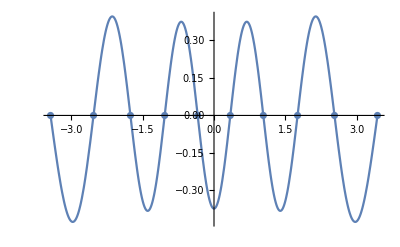

```mathematica
xop // MatrixForm
x[10] //MatrixForm
p1 = Plot[h0eigenfxn[10,x],{x,Min[vals],Max[vals]}];
p2 = ListPlot[Transpose[{vals,{0,0,0,0,0,0,0,0,0,0}}]];
Show[p1,p2]
```

```mathematica
Clear["Global`*"];
adagfxn[n_,m_] := N[Sqrt[m]] /; m-n == 1;
adagfxn[n_,m_] := 0. /; m-n ≠ 1;
adag[basissize_] := Table[adagfxn[n,m],{n,0,basissize-1},{m,0,basissize-1}];
a[basissize_] := ConjugateTranspose[adag[basissize]];
x[basissize_] := Sqrt[1 / 2.](a[basissize] + adag[basissize]);
p[basissize_] := -I Sqrt[2.] (a[basissize] -  adag[basissize]);
h0[basissize_] := DiagonalMatrix[Table[n + 1 / 2,{n, 0, basissize - 1}]] ;
G[basissize_]:= p[basissize].p[basissize]/4 + x[basissize].x[basissize]
H[basissize_]:= -KroneckerProduct[G[basissize],IdentityMatrix[basissize]] + KroneckerProduct[IdentityMatrix[basissize],G[basissize]]
S[basissize_] := Transpose[Normalize /@ Eigenvectors[x[basissize]]];
fn[basissize_,n_] := Sort[Eigenvalues[N[H[basissize]]]][[n]];
toposbasis[basissize_,evec_]:= ConjugateTranspose[S[basissize]].evec;
xvals[basissize_]:= Table[(ConjugateTranspose[S[basissize]].x[basissize].S[basissize])[[m]][[m]],{m,basissize}];
V[x_]:= x^2/2;
```

```mathematica
Eigensystem[H[4].H[4]]
```

{{16.,16.,4.,4.,4.,4.,4.,4.,4.,4.,1.97215×10^-31,1.97215×10^-31,0.,0.,0.,0.},{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}}

```mathematica
N[x/.FindRoot[Normal[Series[Cos[x],{x,0,20}]],{x,1.5},AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->100],20]
```

1.5707963267948966375

```mathematica
N[Pi/2,20]
```

1.5707963267948966192

```mathematica
Kmat[basissize_,T_, t_]:= ConjugateTranspose[S[basissize]].MatrixExp[-I H [basissize](T-t)].S[basissize];
probabilities[basissize_,T_, t_]:= Abs[Kmat[basissize,T, t]]^2;
Kmat2[basissize_,T_,t_,evals_,evecs_]:= Table[Sum[toposbasis[basissize,evecs[[k]]][[x2indx]] Conjugate[toposbasis[basissize,evecs[[k]]][[x1indx]]] Exp[-I evals[[k]] (T-t)],{k,basissize}],{x2indx,basissize},{x1indx,basissize}];
Kan[xf_,tf_]:= Sqrt[1/(2 Pi I Sin[tf])] Exp[I ((xf^2 +1.98166^2) Cos[tf] - 2(-1.98166) xf)/(2 Sin[tf])];
```

(-0.539989-0.455453 ⅈ | -0.107129-0.132097 ⅈ | 0.494102-0.319887 ⅈ | -0.00949522+0.354252 ⅈ
-0.107129-0.132097 ⅈ | -0.539989-0.455453 ⅈ | -0.00949522+0.354252 ⅈ | 0.494102-0.319887 ⅈ
0.494102-0.319887 ⅈ | -0.00949522+0.354252 ⅈ | 0.145348-0.406852 ⅈ | 0.578208-0.0834962 ⅈ
-0.00949522+0.354252 ⅈ | 0.494102-0.319887 ⅈ | 0.578208-0.0834962 ⅈ | 0.145348-0.406852 ⅈ)

(-0.539989-0.455453 ⅈ | -0.107129-0.132097 ⅈ | 0.494102-0.319887 ⅈ | -0.00949522+0.354252 ⅈ
-0.107129-0.132097 ⅈ | -0.539989-0.455453 ⅈ | -0.00949522+0.354252 ⅈ | 0.494102-0.319887 ⅈ
0.494102-0.319887 ⅈ | -0.00949522+0.354252 ⅈ | 0.145348-0.406852 ⅈ | 0.578208-0.0834962 ⅈ
-0.00949522+0.354252 ⅈ | 0.494102-0.319887 ⅈ | 0.578208-0.0834962 ⅈ | 0.145348-0.406852 ⅈ)

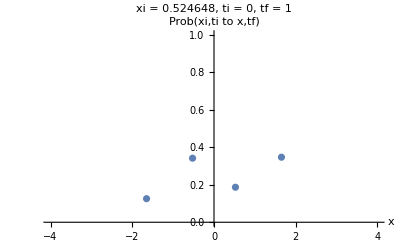

```mathematica
bas = 4; T = 1; t = 0; xx = 3;
{evals,evecs} = Eigensystem[H[bas]];
Kmat[bas,1,0] // MatrixForm
Kmat2[bas,1,0,evals,evecs] // MatrixForm
p1 = ListPlot[Transpose[{xvals[bas],probabilities[bas,T,t][[xx]]}],PlotLabel-> StringForm["xi = ``, ti = ``, tf = ``",xvals[bas][[xx]],t,T],AxesLabel->{"x","Prob(xi,ti to x,tf)"},PlotRange-> {{-4,4},{0,1}}]
```

```mathematica
Table[k,{k,5},{j,5}] // MatrixForm
```

(1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4
5 | 5 | 5 | 5 | 5)

```mathematica
Clear["Global`*"];
bas = 4;
res = {1,0,0,0};
evec = {A,B};
tensored = Flatten[KroneckerProduct[evec,evec]];
tensored // MatrixForm
Solve[Table[res[[k]]==tensored[[k]],{k,bas}],evec]
```

(A^2
A B
A B
B^2)

{{A→-1,B→0},{A→1,B→0}}

```mathematica
Clear["Global`*"];
res ={5.0699219479654735*^-12,-3.3787064904957518*^-09,-3.3787064904957514*^-09,2.2516436477881377*^-06,-3.3787064904957514*^-09,2.2516436477881377*^-06,2.2516436477881377*^-06,-0.0015005444038676391,-3.3787064904957514*^-09,2.2516436477881377*^-06,2.2516436477881377*^-06,-0.0015005444038676391,2.2516436477881377*^-06,-0.0015005444038676391,-0.0015005444038676393,0.9999954967076345};
bas = Sqrt[Length[res]];
evec = Table[a[i],{i,bas}];
tensored = Flatten[KroneckerProduct[evec,evec]];
tensored // MatrixForm;
answer = NSolve[Table[res[[k]]==tensored[[k]],{k,bas}],evec];
evec/.answer[[1]]
```

{-2.25165×10^-6,0.00150055,0.00150055,-0.999998}

```mathematica
(H[4].{-2.2516487177100857*^-6,0.0015005477825741297,0.0015005477825741295,-0.9999977483512823}) / {-2.2516487177100857*^-6,0.0015005477825741297,0.0015005477825741295,-0.9999977483512823}
```

{0.5,1.5,2.5,3.5}